## Initial settings

```mathematica
Dir=NotebookDirectory[];
SetDirectory[Dir];
<<ALPsYBDplotSettings`;
SetDirectory[ToString[StringForm["``../../tab_toPlot/",Dir]]];
```

## Load datasets

```mathematica
dataYlhcb=Import["../Figures/Bound_data/gY/lhcb_gY.csv"];
dataYNA62upper=Import["../Figures/Bound_data/gY/NA62_upperlimit_gY.csv"];
dataYNA62lower=Import["../Figures/Bound_data/gY/NA62_lowerlimit_gY.csv"];
```

```mathematica
reglhcb=ListLinePlot[dataYlhcb,FillingStyle->{Lighter[Orange,0.8]},PlotStyle->None,PlotMarkers->None,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2}},ScalingFunctions->{"Log10","Log10"}, Filling->Top];
```

```mathematica
regna62=ListLinePlot[{dataYNA62upper,dataYNA62lower},FillingStyle->{Lighter[Blue,0.8]},PlotStyle->None,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2}},ScalingFunctions->{"Log10","Log10"}, Filling->{1->{2}}];
```

```mathematica
dataYukawaCHARM=Import["CHARM/alp/CHARM_mX_gY.dat","Table"];
```

```mathematica
dataYukawaHIKE=Import["NA62/alp/NA62_mX_gY.dat","Table"];
dataYukawaSHADOWS=Import["SHADOWS/alp/SHADOWS_mX_gY.dat","Table"];
dataYukawaSHiP=Import["SHiP/alp/SHiP_mX_gY.dat","Table"];
```

```mathematica
dataYukawaDarkQuest=Import["DarkQuest/alp/DarkQuest_mX_gY.dat","Table"];
dataYukawaDUNE=Import["DUNE/alp/DUNE_mX_gY.dat","Table"];
```

```mathematica
dataYukawaHIKEel=Import["NA62/alp/NA62_mX_gY_2El.dat","Table"];
dataYukawaHIKEmu=Import["NA62/alp/NA62_mX_gY_2Mu.dat","Table"];
dataYukawaHIKEleptons=Import["NA62/alp/NA62_mX_gY_2El-2Mu.dat","Table"];
```

## Make plots

```mathematica
YukawaNA62el=CleanContourPlot[ListContourPlot[dataYukawaHIKEel,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Contours->{164.285},ContourStyle->{Dashed,Opacity[0.4,Darker[Red,0.6]]},Evaluate[plotSettings90CLHIKE]]];
YukawaNA62mu=CleanContourPlot[ListContourPlot[dataYukawaHIKEmu,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Contours->{164.285},ContourStyle->{Dotted,Opacity[0.4,Darker[Red,0.6]]},Evaluate[plotSettings90CLHIKE]]];
YukawaNA62=CleanContourPlot[ListContourPlot[dataYukawaHIKE,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Contours->{164.285},Evaluate[plotSettings90CLHIKE]]];
```

```mathematica
YukawaHIKE=CleanContourPlot[ListContourPlot[dataYukawaHIKE,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLHIKE]]];
YukawaSHADOWS=CleanContourPlot[ListContourPlot[dataYukawaSHADOWS,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLSHADOWS]]];
```

```mathematica
YukawaCHARMzoomed=CleanContourPlot[ListContourPlot[dataYukawaCHARM,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLCHARM]]];
```

```mathematica
YukawaCHARM=CleanContourPlot[ListContourPlot[dataYukawaCHARM,PlotRange->{{0.2,3.},{1*10^-8,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLCHARM]]];
YukawaHIKE5=CleanContourPlot[ListContourPlot[dataYukawaHIKE,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLHIKE5]]];
YukawaSHADOWS5=CleanContourPlot[ListContourPlot[dataYukawaSHADOWS,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLSHADOWS5]]];
YukawaSHiP=CleanContourPlot[ListContourPlot[dataYukawaSHiP,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLSHiP]]];
YukawaDarkQuest=CleanContourPlot[ListContourPlot[dataYukawaDarkQuest,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLDarkQuest]]];YukawaDUNE=CleanContourPlot[ListContourPlot[dataYukawaDUNE,PlotRange->{{0.2,3.},{1*10^-7,1*10^-2},{10^-8,Full}},Evaluate[plotSettings90CLDUNE]]];
```

## Print plots

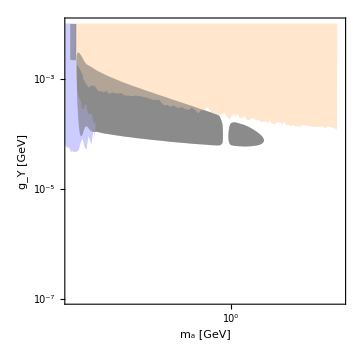

```mathematica
YukawaPast=With[{plotWidth=.75,aspectRatio=.75},display[Show[YukawaCHARMzoomed,regna62,reglhcb,YukawaCHARMzoomed,yLabelxMass[StringForm["``",Style[Subscript["g","Y"],Italic]]]]//at[{0,0},plotWidth],AspectRatio->aspectRatio,ImageSize->500,Epilog->{Inset[baseLegendPast90CL,Scaled[{0.32,0.28}]]}]]
Export[Dir<>"Yukawa_pseudoscalar_Bmeson.pdf",Style[YukawaPast,LineBreakWithin->False]];
```

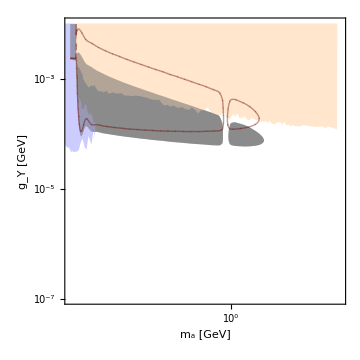

```mathematica
Yukawa=With[{plotWidth=.75,aspectRatio=.75},display[Show[YukawaCHARMzoomed,regna62,reglhcb,YukawaCHARMzoomed,YukawaNA62,YukawaNA62el,YukawaNA62mu,yLabelxMass[StringForm["``",Style[Subscript["g","Y"],Italic]]]]//at[{0,0},plotWidth],AspectRatio->aspectRatio,ImageSize->500,Epilog->{Inset[baseLegendNow90CL,Scaled[{0.35,0.28}]]}]]
Export[Dir<>"ALP_Yukawa_Bmeson_1.4E17.pdf",Style[Yukawa,LineBreakWithin->False]];
```

```mathematica
YukawaLoI=With[{plotWidth=.75,aspectRatio=.75},display[Show[YukawaCHARM,regna62,reglhcb,YukawaCHARM,YukawaHIKE5,YukawaSHADOWS5,yLabelxMass[StringForm["``",Style[Subscript["g","Y"],Italic]]]]//at[{0,0},plotWidth],AspectRatio->aspectRatio,ImageSize->500,Epilog->{Inset[baseLegend90CL,Scaled[{0.34,0.27}]]}]];
RowYukawaLoI=cropVector[YukawaLoI,0,0,400,375]
Export[Dir<>"Yukawa_comparison_LoI.pdf",Style[RowYukawaLoI,LineBreakWithin->False]];
```

-Graphics-

```mathematica
YukawaAll=With[{plotWidth=.75,aspectRatio=.75},display[Show[YukawaCHARM,regna62,reglhcb,YukawaDarkQuest,YukawaDUNE,YukawaCHARM,YukawaHIKE5,YukawaSHADOWS5,YukawaSHiP,yLabelxMass[StringForm["``",Style[Subscript["g","Y"],Italic]]]]//at[{0,0},plotWidth],AspectRatio->aspectRatio,ImageSize->500,Epilog->{Inset[baseLegendAll90CL,Scaled[{0.33,0.32}]]}]];
RowYukawaAll=cropVector[YukawaAll,0,0,400,375]
Export[Dir<>"Yukawa_comparison.pdf",Style[RowYukawaAll,LineBreakWithin->False]];
```

-Graphics-